```mathematica
Solve[x^3+x/w^2-1/w^2==0,x]
```

{{x→-(2/3)^(1/3)/(w^2 (9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))+((9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))/(2^(1/3) 3^(2/3))},{x→(1+ⅈ √3)/(2^(2/3) 3^(1/3) w^2 (9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))-((1-ⅈ √3) (9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))/(2 2^(1/3) 3^(2/3))},{x→(1-ⅈ √3)/(2^(2/3) 3^(1/3) w^2 (9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))-((1+ⅈ √3) (9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))/(2 2^(1/3) 3^(2/3))}}

```mathematica
ecks[w_]:=-(2/3)^(1/3)/(w^2 (9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))+((9/w^2+(√3 √(4+27 w^2))/w^3)^(1/3))/(2^(1/3) 3^(2/3))
```

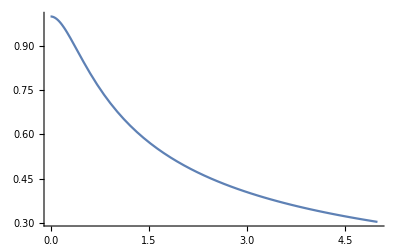

```mathematica
Plot[ecks[w],{w,0,5}]
```